Initialization

```mathematica
FindDates[StartDatei_DateObject,EndDatei_DateObject,DayTypei_]:=Module[{day,StartDate=StartDatei,EndDate=EndDatei,DayType=ToExpression@DayTypei,Dates},
For[day=StartDate;Dates={},day≤ EndDate,day=DatePlus[day,1],
If[Or@@(DayMatchQ[day,#] &/@DayType), AppendTo[Dates,day]]
];
Dates
]

AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);

opts={
AspectRatio->0.2,
GridLines->{Automatic,None},
AxesOrigin->Center,
PlotLayout->"Grouped",
GridLines->{Sundays, None}
};
```

## Seminar Planning

```mathematica
SemesterStartDate=<|"date"->DateObject[{2018,1,24}],"Comment"->"First Day of Classes"|>;

SemesterEndDate=<|"date"->DateObject[{2018,5,9}],"Comment"->"Classes end"|>;

HolidayDates=Dataset[<|"Holidays"->{
<|"date"->DateObject[{2018,3,26}],"Comment"->"SpringBreak"|>,
<|"date"->DateObject[{2018,2,20}],"Comment"->"Long Weekend"|>}|>];
Echo[HolidayDates//Sort,"Holday Dates\n"];
AutoCollapse[]
```

Holday Dates
 Dataset[<>]

```mathematica
DatesTaken=Dataset[<|"Leslie"->
<|"date"->DateObject[{2018,02,05}],"Speaker"->"Leslie Lambertson","Afflication"->"Drexel University"|>,
"Guy"->
<|"date"->DateObject[{2018,03,19}],"Speaker"->"Guy Genin",
"Afflication"->"Washington University in St. Louis","website"->Hyperlink["http://www.cemb.org"]|>,
"Marina"-><|"date"->DateObject[{2018,02,12}],"Speaker"->"Marina Leite","Afflication"->"University of Maryland"|>,
"Mitra"-><|"date"->DateObject["Feb 26, 2018"],"Speaker"->"Mitra Taheri"|>,
"Tal"-><|"date"->DateObject[{2018,03,05}],"Speaker"->"Tal Cohen","Afflication"->"MIT"|>,
"Maryam"-><|"date"->DateObject[{2018,01,29}],"Speaker"->"Maryam  Ghazisaeidi","Afflication"->"Ohio State University"|>,
"Veronica"-><|"date"->DateObject[{2018,05,07}],"Speaker"->"Veronica Eliasson","Afflication"->"UCSD"|>,
"Maurizio"-><|"date"->DateObject["April 9th, 2018"],"Speaker"->"Maurizio M. Chiaramonte","Afflication"->"Princeton"|>
|>];
Echo[DatesTaken//Sort,"Dates Taken\n"];
AutoCollapse[]
```

Dates Taken
 Dataset[<>]

```mathematica
For[day=SemesterStartDate["date"];AvailableSeminarDates={},
day≤ SemesterEndDate["date"],
day=DatePlus[day,1],
If[DayMatchQ[day,Monday] &&  
                !MemberQ[Table[HolidayDates[[i]]["date"],{i,1,Length@HolidayDates}],day] && 
                !MemberQ[Table[DatesTaken[i,"date"],{i,1,Length@DatesTaken}],day], AppendTo[AvailableSeminarDates,day]]];
(*Echo[Multicolumn[Map[DateString[#,{"DayName", "  ","Month","/","Day","/","YearShort"}] &, AvailableSeminarDates],1],"Available Seminar Dates \n"];*)
Echo[Multicolumn[Map[DateString[#,{"Month","/","Day","/","YearShort"}] &, AvailableSeminarDates],1],"Available Seminar Dates \n"];
AutoCollapse[]
```

Available Seminar Dates 
 02/19/18
03/12/18
03/26/18
04/02/18
04/16/18
04/23/18
04/30/18

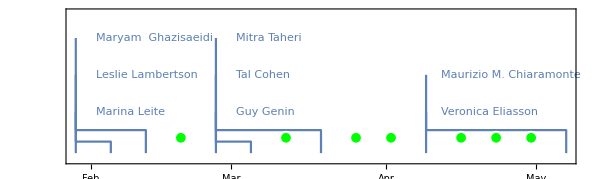

```mathematica
plt2=TimelinePlot[AvailableSeminarDates,PlotStyle->{Green,Circle[]}];
plt1=TimelinePlot@Apply[Association,Table[DatesTaken[i,"Speaker"]->DatesTaken[i,"date"],{i,1,Length[DatesTaken[;;,"date"]]}]];
Show[plt1,plt2]
AutoCollapse[]
```

Comment on  Dec 26, 6:31 pm. I need to check the above dates with email sent out by Prof. Kumar.

## General Planning

Appointments

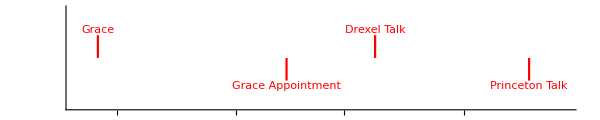

```mathematica
Appointments=<|
"Grace"-><|"date"->DateObject["Dec 27, 2017"]|>,
"Princeton Talk"-><|"date"->DateObject["April 18, 2018"]|>,
"Grace Appointment"-><|"date"->DateObject["Feb 14, 2018"]|>,
"Drexel Talk"-><|"date"->DateObject["March 9, 2018"]|>
|>;

Aplt=(TimelinePlot[Appointments[[;;,"date"]],PlotStyle->{Red,Opacity[1]},##,GridLines->{Sundays, None},GridLinesStyle->Directive[Green,Thickness[0.0063],Opacity[0.2]]]&)@@opts
AutoCollapse[]
```

Events

```mathematica
Events:=<|
Text[Style["Today",Red,Italic,14]]-><|"date"->Now|>,
"Saurabhi returns"-><|"date"->DateObject["Dec 28, 2017"]|>,
"Final Project"-><|"date"->DateObject["Dec 19, 2017"]|>,
"Wenqiang Leaves"-><|"date"->DateObject["Dec 25, 2017"]|>,
"Wenqiang Returns"-><|"date"->DateObject["Jan 6, 2018"]|>,
"Max  Leaves"-><|"date"->DateObject["Dec 22, 2017"]|>,
"Max Returns"-><|"date"->DateObject["Jan 15, 2018"]|>,
"Joyce  Leaves"-><|"date"->DateObject["Dec 24, 2017"]|>,
"Joyce Returns"-><|"date"->DateObject["Jan 10, 2018"]|>,
"Kauhsik  Leaves"-><|"date"->DateObject["Jan 28, 2018"]|>,
"Kauhsik Returns"-><|"date"->DateObject["Feb 6 2018"]|>,
"Pyara Bday"-><|"date"->DateObject["March 24, 2018"]|>,
"Pyari Bday"-><|"date"->DateObject["March 14, 2018"]|>,
"Austin Trip"-><|"date"->DateObject["Feb 18, 2018"]|>
|>;
Eplt:=(TimelinePlot[Events[[;;,"date"]],PlotStyle->{Blue,Opacity[1]},##]&)@@opts
AutoCollapse[]
```

SeminarDates

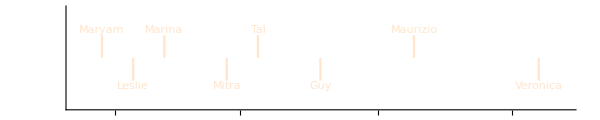

```mathematica
SeminarDatesTaken=<|
"Leslie"->
<|"date"->DateObject[{2018,02,05}],"Speaker"->"Leslie Lambertson","Afflication"->"Drexel University"|>,
"Guy"->
<|"date"->DateObject[{2018,03,19}],"Speaker"->"Guy Genin",
"Afflication"->"Washington University in St. Louis","website"->Hyperlink["http://www.cemb.org"]|>,
"Marina"-><|"date"->DateObject[{2018,02,12}],"Speaker"->"Marina Leite","Afflication"->"University of Maryland"|>,
"Mitra"-><|"date"->DateObject["Feb 26, 2018"],"Speaker"->"Mitra Taheri"|>,
"Tal"-><|"date"->DateObject[{2018,03,05}],"Speaker"->"Tal Cohen","Afflication"->"MIT"|>,
"Maryam"-><|"date"->DateObject[{2018,01,29}],"Speaker"->"Maryam  Ghazisaeidi","Afflication"->"Ohio State University"|>,
"Veronica"-><|"date"->DateObject[{2018,05,07}],"Speaker"->"Veronica Eliasson","Afflication"->"UCSD"|>,
"Maurizio"-><|"date"->DateObject["April 9th, 2018"],"Speaker"->"Maurizio M. Chiaramonte","Afflication"->"Princeton"|>
|>;
(*SemPlt=(TimelinePlot[Events2[[#]][[;;,"date"]]&/@{"Seminars"},PlotStyle->{Orange,Opacity[0.2]},##]&)@@opts*)
SemPlt=(TimelinePlot[SeminarDatesTaken[[;;,"date"]],PlotStyle->{Orange,Opacity[0.2]},##]&)@@opts
AutoCollapse[]
```

Prof.  Maryam Ghazisaeidi (Ohio State University): January 29, 2018 (Monday)
Prof. Marina Leite (University of Maryland): February 12, 2018 (Monday)
Prof. Mitra Taheri (Drexel University):  February 26, 2018 (Monday)
Prof. Yue Qi (Michigan State University): March 08, 2018 (Thursday)

Holidays

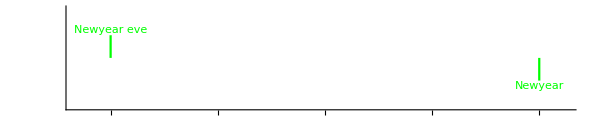

```mathematica
Holidays=<|
"Newyear"-><|"date"->DateObject["Jan 1, 2018"],"PltStyle"->{Red}|>,
"Newyear eve"-><|"date"->DateObject["Dec 31, 2017"],"PltStyle"->{Red}|>|>;

HolPlt=(TimelinePlot[Holidays[[;;,"date"]],PlotStyle->{Green,Opacity[1]},##]&)@@opts
AutoCollapse[]
```

Days of the Week

```mathematica
t=Now;
Sundays=FindDates[Tomorrow,DateObject["May 1, 2018"],{Sunday}];
Saturdays=FindDates[Tomorrow,DateObject["May 1, 2018"],{Saturday}];
Mondays=FindDates[Tomorrow,DateObject["May 1, 2018"],{Monday}];
Tuesdays=FindDates[Tomorrow,DateObject["May 1, 2018"],{Tuesday}];
Wednesdays=FindDates[Tomorrow,DateObject["May 1, 2018"],{Wednesday}];
Thursdays=FindDates[Tomorrow,DateObject["May 1, 2018"],{Thursday}];
Fridays=FindDates[Tomorrow,DateObject["May 1, 2018"],{Friday}];


mplt=(TimelinePlot[Mondays,PlotMarkers->Graphics[{Black,Opacity[0.5],Rectangle[]}],##]&)@@opts;
tplt=(TimelinePlot[Tuesdays,PlotMarkers->Graphics[{Brown,Opacity[0.5],Rectangle[]}],##]&)@@opts;
wplt=(TimelinePlot[Wednesdays,PlotMarkers->Graphics[{Gray,Opacity[0.5],Rectangle[]}],##]&)@@opts;
thplt=(TimelinePlot[Thursdays,PlotMarkers->Graphics[{Blue,Opacity[0.5],Rectangle[]}],##]&)@@opts;
fplt=(TimelinePlot[Fridays,PlotMarkers->Graphics[{Orange,Opacity[0.5],Rectangle[]}],##]&)@@opts;
splt=(TimelinePlot[Saturdays,PlotMarkers->Graphics[{Green,Opacity[0.5],Rectangle[]}],##]&)@@opts;

Print[Text@Style["Defined Days of the Week at ",FontSize->12,Bold,FontFamily->"Consolas"] ,DateString[Now]]

AutoCollapse[]
```

Defined Days of the Week at Mon 12 Feb 2018 21:24:10

Master Time Line

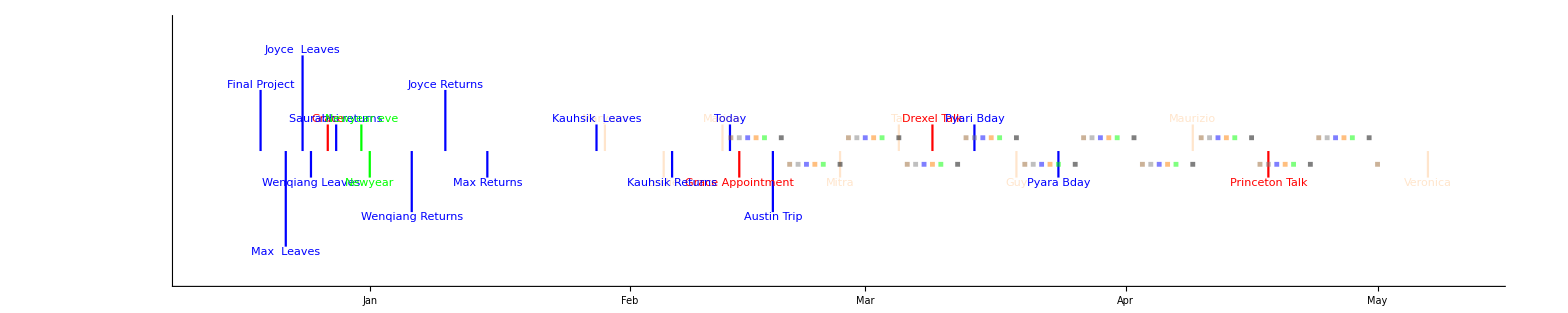

```mathematica
Show[Aplt,SemPlt,Eplt,mplt,tplt,wplt,thplt,fplt,splt,HolPlt,ImageSize->2000,PlotRange->All]
AutoCollapse[]
```

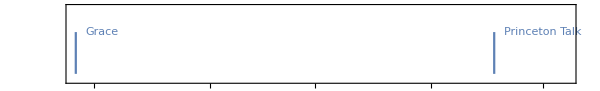

```mathematica
Appointments2=<|
"Grace"-><|"date"->DateObject["Dec 27, 2017"],"Details"->Text["Hellow \nThis is how the world is"]|>,
"Princeton Talk"-><|"date"->DateObject["April 18, 2018"],"Details"->Hyperlink["Wolfram Research, Inc.", "message://%3c46E3DE82-99AC-4BFB-A36F-B8D6D7FABEE1@brown.edu"]|>
|>;

TimelinePlot[Apply[Association,Table[Keys[Appointments2][[i]]->PopupWindow[Appointments2[[i,"date"]],Appointments2[[i,"Details"]]],{i,1,Length@Appointments2}]]]
AutoCollapse[]
```

## Trash

```mathematica
Events2=<|
"Appointments"->Appointments,
"Events"->Events,
"Weekends"->Inner[Interval[{#1,#2}]&,Saturdays,Sundays,List],
"Holidays"->Holidays,
"Seminars"->SeminarDatesTaken
|>;
```

Open Scifler Letter

```mathematica
ClPath = StringJoin[" NotebookOpen@CloudObject[\"", 
  StringCases[Apply[ToString, NotebookFileName[]], 
    x__ ~~ "ca1/" ~~ y__~~".nb"~~___ -> y],".nb", "\"] "]
AutoCollapse[]
```

NotebookOpen@CloudObject[".nb"]